## Mathematica: getting started

Good news: if you are reading this notebook, then you have successfully installed and opened Mathematica.

So, what next? Click on “File” at the top of your screen, then choose “New”, then choose “Notebook”.

This will open a new Mathematica notebook for you to work in. It should look like a blank white screen. To start using Mathematica, click anywhere on the notebook, and simply start typing. I recommend starting with something simple, say 2 + 2.

```mathematica
2 +2
```

To then evaluate something in Mathematica, click next to what you’ve typed, and then press ⇧[⌤]. (Hold down the “Shift” key, and then press “Enter”.)

NOTE: IF THIS DOES NOT WORK, PLEASE CONTACT US! Something may be wrong with your installation of Mathematica.

```mathematica
2 + 2
```

4

## Mathematica: Functions

All calculations done in Mathematica are done by calling functions. 

You can think of each function as a box. Into each box, we put arguments, and then the box spits out a result:

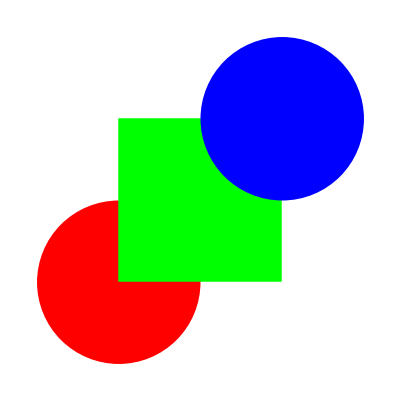
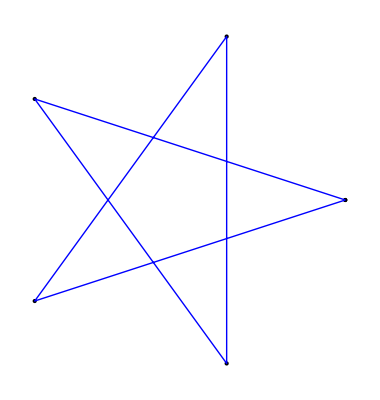
-Graphics-argument(s) → -Graphics3D-function → -Graphics-result

#### Evaluate the following examples:

(Click next to the inputs below, hold down Shift, and push Enter.)

```mathematica
Sin[Pi/2]
```

```mathematica
Expand[(a + b)^2]
```

In the two examples above, each function (Sin and Expand) took just one argument. In the first case, the argument was Pi/2, in the second case, the argument was (a + b)^2.

In the following example, we will use two arguments. In this case, the first argument is the image to edit, and the second argument (the number 200) is the size (in pixels) of the region to extract from the center of the image. The image in the result will have dimensions 200 pixels x 200 pixels.

```mathematica
ImageCrop[-Graphics-,200]
```

And in the next example, we will use zero arguments!

```mathematica
RandomInteger[]
```

So, functions can have any number of arguments (including zero arguments).

#### Challenge question: Can you think of a function that can have any number of arguments?

A function that can have any number of arguments is: (your answer here)

#### Challenge question: Looking at the above examples, finish the sentence below by describing the proper syntax for every function.

The proper syntax for every function is: (your answer here)

#### Curve ball!

By now, you’ve guessed the syntax for every function entered into Mathematica. So, addition should look like this:

```mathematica
Plus[2, 2]
```

But wait! Earlier, we typed “2 + 2” into Mathematica, and got the correct answer. So, are there different ways to enter functions into Mathematica?

Yes. 

Many functions have a shorthand notation that matches common arithmetic notation. Internally within Mathematica, however, everything is represented in the function notation we discovered above. So, when you type “2 + 2”, Mathematica interprets this as Plus[2, 2] and then evaluates.

Very important note: EVERYTHING in Mathematica is represented as head[arguments].

Here are common shortcuts:

x+y+z | add
-x | minus (negative)
x-y | subtract
x y z or x⋆y⋆z | multiply
x/y | divide
x^y | power
x (y+z) | grouping

Note: Mathematica interprets a space between two numbers or symbols as multiplication. So: 2 3 is the same as 2*3. 

It is good practice to use the explicit times operator (*) to make your code easier to read.

#### Challenge question: We know that the “function notation” form of two plus two is Plus[2, 2]. What is the “function notation” form of two times two?

The “function notation” of two times two is: (your answer here)

#### Challenge questions: Guess the “function notation” form for each of the following:

```mathematica
- x
```

The function notation form is: (your answer here)

```mathematica
x - y
```

The function notation form is: (your answer here)

```mathematica
x (y + z)
```

The function notation form is: (your answer here)

## Mathematica documentation is wonderful!

At any time, should you have any questions, I highly recommend the Mathematica documentation - I use it all the time! To access it, click “Help” at the top of your screen, and then click on “Documentation center”.

If you have a question about any function in particular, just open a new cell in Mathematica, and type “?” followed by the function name, and then evaluate.

```mathematica
?Plus
```

x+y+z represents a sum of terms.

At the bottom of the ouput cell (the line just above that says “x + y + z represents a sum of terms”), you should see two arrows pointing right. If you click on this, it will open a new window and take you straight to the Documentation page about this function (example picture below).

#### Assignment:

Read the documentation for the function called Sum, and demonstrate it below.

## Arithmetic and Math Functions

Let’s do some math with Mathematica!

### Basic: Mathematica is like a calculator

Suppose you went out to eat, and the service was amazing. The meal cost $38.72. How much does it cost with a 20% tip?

```mathematica
38.72 + .2*38.72
```

46.464

#### Challenge question: Same meal, but the service wasn’t so good. What does it cost with a 15% tip?

### More interesting: Mathematica is like a calculator-turned-superhero

What is the x-intercept of the line y == 5 x - 3? (So - let’s solve 0 == 5 x - 3.)

Hmmm... how do we solve this? Well, we could do:

```mathematica
0 == 5 x - 3
3 == 5 x
3 / 5 == x
```

Or, we could just use the function Solve:

```mathematica
Solve[0 == 5x - 3, x]
```

{{x→3/5}}

The formatting of the result looks a bit odd - but we’ll worry more about that later!

#### Challenge question: What are the roots of x^2 + 5 x - 3?

### Even more interesting: Mathematica is like a calculator-turned-superhero-turned-artist!

We know where to find the root of the line 5 x - 3. But let’s see what the line looks like on the whole interval from -1 to 1.

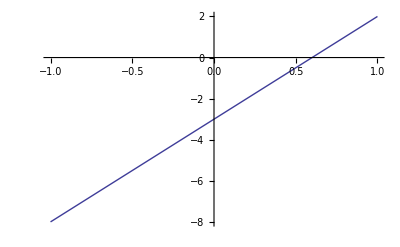

```mathematica
Plot[5 x - 3, {x, -1, 1}]
```

OK, that was nice - but not incredibly interesting!

#### Challenge question

Plot the function  x^2 + 5 x - 3 on the interval -10 to 10.

#### Challenge question

Familiarize yourself with the function Plot3D, and, using Plot or Plot3D, plot a function of your choice to share with the class.

## Lists and Map

Lists are used in Mathematica to represent vectors, matrices, and data. They are also used as function arguments.

Here is an example of a List:

```mathematica
{1,2,3}
```

We have seen a List before:

```mathematica
Plot[x, {x, -1, 1}]
```

The above is an example of how Lists are used to help group arguments together for functions.

Here is another example of a List:

```mathematica
{{1,2,3}, {4,5,6}}
```

The above nested lists can represent a matrix:

```mathematica
MatrixForm[{{1,2,3}, {4,5,6}}]
```

(1 | 2 | 3
4 | 5 | 6)

NOTE: MatrixForm is only a formatting function, so you can see your nested Lists as a matrix. This means that it should only be used for displaying results - not for computation!

NOTE: The function-argument form of a List is:

```mathematica
List[1,2,3]
```

Let’s learn a new Mathematica function that is tailored specifically for Lists.

```mathematica
?Map
```

Map[f,expr] or f/@expr applies f to each element on the first level in expr. 
Map[f,expr,levelspec] applies f to parts of expr specified by levelspec.

The documentation is a bit hard to read. Let’s just look at an example. First, let’s see the function Reverse. This takes a List as its argument, and returns the List reversed - from the last element to the first.

```mathematica
Reverse[{1,2,3}]
```

{3,2,1}

What if we had a List of Lists (a matrix)? Say,

```mathematica
{{1,2,3}, {4,5,6}, {7,8,9}}
```

And what if we wanted to reverse all of those lists (the rows of the matrix)? We could use the function Map to reverse each of the lists:

```mathematica
Map[Reverse, {{1,2,3}, {4,5,6}, {7,8,9}}]
```

{{3,2,1},{6,5,4},{9,8,7}}

And then we could even Reverse the List of (reversed) Lists, if we’d like:

```mathematica
Reverse[{{3,2,1},{6,5,4},{9,8,7}}]
```

{{9,8,7},{6,5,4},{3,2,1}}

#### Challenge question: Do the above with the function Sort instead of Reverse. Show each step in Matrix form.

## Quiz!

Fill in the blank!
	All calculations are done in Mathematica by calling (your answer here)
	Into Mathematica functions, we put (your answer here)
	The window that Mathematica calculations are typed into is called a (your answer here)

Describe the syntax of a Mathematica function.
(your answer here)

Using the Mathematica documentation, create an image using the function Graphics.
	Note the use of Lists in Graphics arguments!

```mathematica
?Graphics
```

Graphics[primitives,options] represents a two-dimensional graphical image.

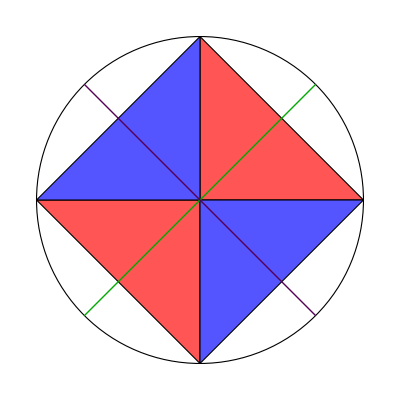

```mathematica
Graphics[{
	EdgeForm[Black], White, Disk[{0,0}, 1], 
	Lighter[Red], Polygon[{{0, -1}, {-1,0}, {1,0}, {0, 1} }],
	Lighter[Blue], Polygon[{ {-1,0}, {1,0},{0, -1}, {0, 1} }],
	Thick, Darker[Green], Line[{{-Cos[Pi/4], -Sin[Pi/4]}, {Cos[Pi/4], Sin[Pi/4]}}],
	Thick, Darker[Purple], Line[{{-Cos[Pi/4], Sin[Pi/4]}, {Cos[Pi/4], -Sin[Pi/4]}}]
}]
```